# HAProxy

## Analysis Notebook

## Setup

```mathematica
Needs["HAProxy`"];
```

```mathematica
Needs["Utilities`CSV`"];
```

```mathematica
Needs["Utilities`UnixTime`"];
```

```mathematica
Needs["Utilities`Debug`"]
```

## Analysis

```mathematica
dataPath=FileNameJoin[{ProjectDirectory["HAProxy`"],"TestData"}];
```

```mathematica
haproxyDataFileNamePattern="haproxyDataList_"~~t1:DigitCharacter..~~"_"~~t2:DigitCharacter..~~".csv";
```

```mathematica
FileNames[haproxyDataFileNamePattern,{dataPath}]
```

{/Users/matt/WolframWorkspaces/Base2/HAProxy/TestData/haproxyDataList_1389065284037_1389066915781.csv}

```mathematica
haproxyDataListFileName="haproxyDataList_1389065284037_1389066915781.csv";
```

```mathematica
haproxyDataListFilePath=FileNameJoin[{dataPath,haproxyDataListFileName}];
```

```mathematica
haproxyDataList=Import[haproxyDataListFilePath];
```

```mathematica
haproxyDataList//Length
```

4897

```mathematica
haproxyDataList[[;;10]]//TableForm
```

timestamp | # pxname | svname | qcur | qmax | scur | smax | slim | stot | bin | bout | dreq | dresp | ereq | econ | eresp | wretr | wredis | status | weight | act | bck | chkfail | chkdown | lastchg | downtime | qlimit | pid | iid | sid | throttle | lbtot | tracked | type | rate | rate_lim | rate_max | check_status | check_code | check_duration | hrsp_1xx | hrsp_2xx | hrsp_3xx | hrsp_4xx | hrsp_5xx | hrsp_other | hanafail | req_rate | req_rate_max | req_tot | cli_abrt | srv_abrt | 
1389065284037 | http-in | FRONTEND |  |  | 1 | 198 | 3000 | 80041 | 10013685 | 13668168 | 0 | 0 | 0 |  |  |  |  | OPEN |  |  |  |  |  |  |  |  | 1 | 1 | 0 |  |  |  | 0 | 2 | 0 | 1405 |  |  |  | 0 | 79988 | 0 | 52 | 0 | 0 |  | 2 | 1410 | 80041 |  |  | 
1389065284037 | backend_vagrantx_cloud_appcelerator_com | 1 | 0 | 0 | 0 | 174 |  | 79976 | 9992125 | 13589290 |  | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 | 0 | 0 | 2483 | 0 |  | 1 | 2 | 1 |  | 79937 |  | 2 | 0 |  | 1410 | L4OK |  | 0 | 0 | 79937 | 0 | 0 | 0 | 0 | 0 |  |  |  | 101 | 0 | 
1389065284037 | backend_vagrantx_cloud_appcelerator_com | BACKEND | 0 | 0 | 0 | 174 | 0 | 79937 | 9992125 | 13589290 | 0 | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 |  | 0 | 2483 | 0 |  | 1 | 2 | 0 |  | 79937 |  | 1 | 0 |  | 1410 |  |  |  | 0 | 79937 | 0 | 0 | 0 | 0 |  |  |  |  | 101 | 0 | 
1389065285139 | http-in | FRONTEND |  |  | 1 | 198 | 3000 | 80043 | 10013970 | 13669367 | 0 | 0 | 0 |  |  |  |  | OPEN |  |  |  |  |  |  |  |  | 1 | 1 | 0 |  |  |  | 0 | 1 | 0 | 1405 |  |  |  | 0 | 79989 | 0 | 53 | 0 | 0 |  | 1 | 1410 | 80043 |  |  | 
1389065285139 | backend_vagrantx_cloud_appcelerator_com | 1 | 0 | 0 | 0 | 174 |  | 79976 | 9992125 | 13589290 |  | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 | 0 | 0 | 2485 | 0 |  | 1 | 2 | 1 |  | 79937 |  | 2 | 0 |  | 1410 | L4OK |  | 0 | 0 | 79937 | 0 | 0 | 0 | 0 | 0 |  |  |  | 101 | 0 | 
1389065285139 | backend_vagrantx_cloud_appcelerator_com | BACKEND | 0 | 0 | 0 | 174 | 0 | 79937 | 9992125 | 13589290 | 0 | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 |  | 0 | 2485 | 0 |  | 1 | 2 | 0 |  | 79937 |  | 1 | 0 |  | 1410 |  |  |  | 0 | 79937 | 0 | 0 | 0 | 0 |  |  |  |  | 101 | 0 | 
1389065286021 | http-in | FRONTEND |  |  | 1 | 198 | 3000 | 80045 | 10014255 | 13670566 | 0 | 0 | 0 |  |  |  |  | OPEN |  |  |  |  |  |  |  |  | 1 | 1 | 0 |  |  |  | 0 | 3 | 0 | 1405 |  |  |  | 0 | 79990 | 0 | 54 | 0 | 0 |  | 3 | 1410 | 80045 |  |  | 
1389065286021 | backend_vagrantx_cloud_appcelerator_com | 1 | 0 | 0 | 0 | 174 |  | 79976 | 9992125 | 13589290 |  | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 | 0 | 0 | 2485 | 0 |  | 1 | 2 | 1 |  | 79937 |  | 2 | 0 |  | 1410 | L4OK |  | 0 | 0 | 79937 | 0 | 0 | 0 | 0 | 0 |  |  |  | 101 | 0 | 
1389065286021 | backend_vagrantx_cloud_appcelerator_com | BACKEND | 0 | 0 | 0 | 174 | 0 | 79937 | 9992125 | 13589290 | 0 | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 |  | 0 | 2485 | 0 |  | 1 | 2 | 0 |  | 79937 |  | 1 | 0 |  | 1410 |  |  |  | 0 | 79937 | 0 | 0 | 0 | 0 |  |  |  |  | 101 | 0 |

```mathematica
haproxyHeader=haproxyDataList[[1]]
```

{timestamp,# pxname,svname,qcur,qmax,scur,smax,slim,stot,bin,bout,dreq,dresp,ereq,econ,eresp,wretr,wredis,status,weight,act,bck,chkfail,chkdown,lastchg,downtime,qlimit,pid,iid,sid,throttle,lbtot,tracked,type,rate,rate_lim,rate_max,check_status,check_code,check_duration,hrsp_1xx,hrsp_2xx,hrsp_3xx,hrsp_4xx,hrsp_5xx,hrsp_other,hanafail,req_rate,req_rate_max,req_tot,cli_abrt,srv_abrt,}

```mathematica
haproxyCsvIndex=MakeCsvIndex[haproxyHeader];
```

```mathematica
Map[haproxyCsvIndex[#]&,haproxyHeader]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53}

```mathematica
plotData=Map[{DateList[UnixTime[#[[1]]]],Sequence@@#[[2;;]]}&,Select[haproxyDataList,StringMatchQ[#[[haproxyCsvIndex["# pxname"]]],"backend_vagrantx_cloud_appcelerator_com"]&&MatchQ[#[[haproxyCsvIndex["svname"]]],1]&]];
```

```mathematica
plotData//Length
```

1632

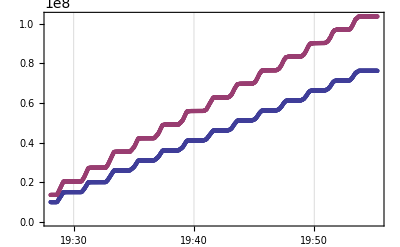

```mathematica
DateListPlot[{plotData[[All,haproxyCsvIndex[{"timestamp","bin"}]]],plotData[[All,haproxyCsvIndex[{"timestamp","bout"}]]]}]
```

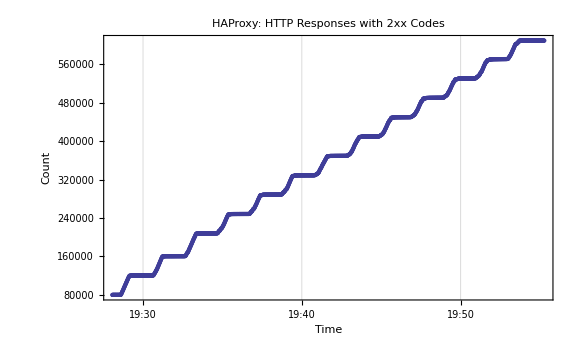

```mathematica
hrsp2xxPlot=DateListPlot[plotData[[All,haproxyCsvIndex[{"timestamp","hrsp_2xx"}]]],PlotRange->All,Joined->False,Axes->False,Frame->True,FrameLabel->{Style["Time",12],Style["Count",12]},PlotLabel->Style["HAProxy: HTTP Responses with 2xx Codes",20],ImageSize->8 72]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop","hrsp2xxPlot.png"}],hrsp2xxPlot]
```

/Users/matt/Desktop/hrsp2xxPlot.png

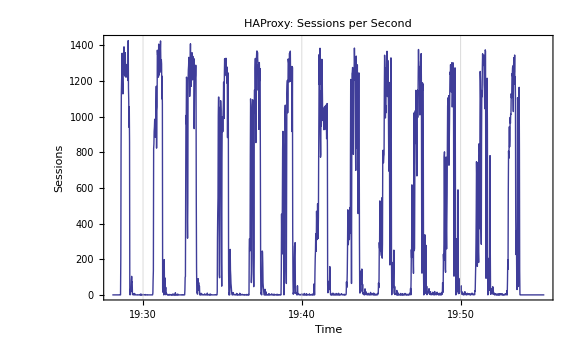

```mathematica
sessionsPerSecondPlot=DateListPlot[plotData[[All,haproxyCsvIndex[{"timestamp","rate"}]]],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{Style["Time",12],Style["Sessions",12]},PlotLabel->Style["HAProxy: Sessions per Second",20],ImageSize->8 72]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop","sessionsPerSecondPlot.png"}],sessionsPerSecondPlot]
```

/Users/matt/Desktop/sessionsPerSecondPlot.png

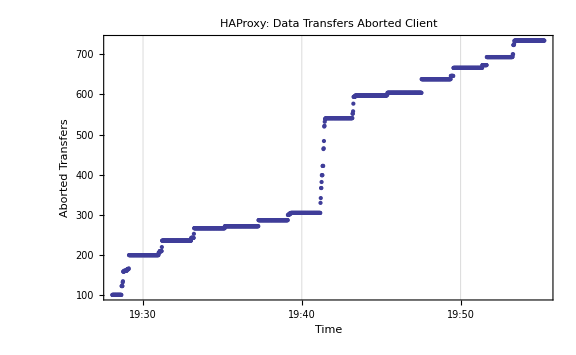

```mathematica
abortedTransfersPlot=DateListPlot[plotData[[All,haproxyCsvIndex[{"timestamp","cli_abrt"}]]],PlotRange->All,Joined->False,Axes->False,Frame->True,FrameLabel->{Style["Time",12],Style["Aborted Transfers",12]},PlotLabel->Style["HAProxy: Data Transfers Aborted Client",20],ImageSize->8 72]
```

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Desktop","abortedTransfersPlot.png"}],abortedTransfersPlot]
```

/Users/matt/Desktop/abortedTransfersPlot.png

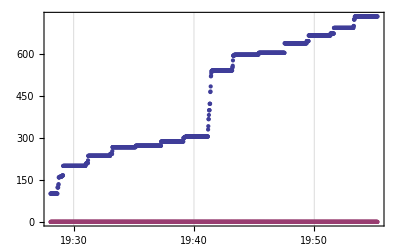

```mathematica
DateListPlot[{plotData[[All,haproxyCsvIndex[{"timestamp","cli_abrt"}]]],plotData[[All,haproxyCsvIndex[{"timestamp","srv_abrt"}]]]}]
```

```mathematica
haproxyDataList[[;;10]]//TableForm
```

timestamp | # pxname | svname | qcur | qmax | scur | smax | slim | stot | bin | bout | dreq | dresp | ereq | econ | eresp | wretr | wredis | status | weight | act | bck | chkfail | chkdown | lastchg | downtime | qlimit | pid | iid | sid | throttle | lbtot | tracked | type | rate | rate_lim | rate_max | check_status | check_code | check_duration | hrsp_1xx | hrsp_2xx | hrsp_3xx | hrsp_4xx | hrsp_5xx | hrsp_other | hanafail | req_rate | req_rate_max | req_tot | cli_abrt | srv_abrt | 
1389065284037 | http-in | FRONTEND |  |  | 1 | 198 | 3000 | 80041 | 10013685 | 13668168 | 0 | 0 | 0 |  |  |  |  | OPEN |  |  |  |  |  |  |  |  | 1 | 1 | 0 |  |  |  | 0 | 2 | 0 | 1405 |  |  |  | 0 | 79988 | 0 | 52 | 0 | 0 |  | 2 | 1410 | 80041 |  |  | 
1389065284037 | backend_vagrantx_cloud_appcelerator_com | 1 | 0 | 0 | 0 | 174 |  | 79976 | 9992125 | 13589290 |  | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 | 0 | 0 | 2483 | 0 |  | 1 | 2 | 1 |  | 79937 |  | 2 | 0 |  | 1410 | L4OK |  | 0 | 0 | 79937 | 0 | 0 | 0 | 0 | 0 |  |  |  | 101 | 0 | 
1389065284037 | backend_vagrantx_cloud_appcelerator_com | BACKEND | 0 | 0 | 0 | 174 | 0 | 79937 | 9992125 | 13589290 | 0 | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 |  | 0 | 2483 | 0 |  | 1 | 2 | 0 |  | 79937 |  | 1 | 0 |  | 1410 |  |  |  | 0 | 79937 | 0 | 0 | 0 | 0 |  |  |  |  | 101 | 0 | 
1389065285139 | http-in | FRONTEND |  |  | 1 | 198 | 3000 | 80043 | 10013970 | 13669367 | 0 | 0 | 0 |  |  |  |  | OPEN |  |  |  |  |  |  |  |  | 1 | 1 | 0 |  |  |  | 0 | 1 | 0 | 1405 |  |  |  | 0 | 79989 | 0 | 53 | 0 | 0 |  | 1 | 1410 | 80043 |  |  | 
1389065285139 | backend_vagrantx_cloud_appcelerator_com | 1 | 0 | 0 | 0 | 174 |  | 79976 | 9992125 | 13589290 |  | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 | 0 | 0 | 2485 | 0 |  | 1 | 2 | 1 |  | 79937 |  | 2 | 0 |  | 1410 | L4OK |  | 0 | 0 | 79937 | 0 | 0 | 0 | 0 | 0 |  |  |  | 101 | 0 | 
1389065285139 | backend_vagrantx_cloud_appcelerator_com | BACKEND | 0 | 0 | 0 | 174 | 0 | 79937 | 9992125 | 13589290 | 0 | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 |  | 0 | 2485 | 0 |  | 1 | 2 | 0 |  | 79937 |  | 1 | 0 |  | 1410 |  |  |  | 0 | 79937 | 0 | 0 | 0 | 0 |  |  |  |  | 101 | 0 | 
1389065286021 | http-in | FRONTEND |  |  | 1 | 198 | 3000 | 80045 | 10014255 | 13670566 | 0 | 0 | 0 |  |  |  |  | OPEN |  |  |  |  |  |  |  |  | 1 | 1 | 0 |  |  |  | 0 | 3 | 0 | 1405 |  |  |  | 0 | 79990 | 0 | 54 | 0 | 0 |  | 3 | 1410 | 80045 |  |  | 
1389065286021 | backend_vagrantx_cloud_appcelerator_com | 1 | 0 | 0 | 0 | 174 |  | 79976 | 9992125 | 13589290 |  | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 | 0 | 0 | 2485 | 0 |  | 1 | 2 | 1 |  | 79937 |  | 2 | 0 |  | 1410 | L4OK |  | 0 | 0 | 79937 | 0 | 0 | 0 | 0 | 0 |  |  |  | 101 | 0 | 
1389065286021 | backend_vagrantx_cloud_appcelerator_com | BACKEND | 0 | 0 | 0 | 174 | 0 | 79937 | 9992125 | 13589290 | 0 | 0 |  | 0 | 0 | 39 | 0 | UP | 1 | 1 | 0 |  | 0 | 2485 | 0 |  | 1 | 2 | 0 |  | 79937 |  | 1 | 0 |  | 1410 |  |  |  | 0 | 79937 | 0 | 0 | 0 | 0 |  |  |  |  | 101 | 0 |

```mathematica
Join[{haproxyHeader},haproxyDataList[[-10;;]]]//TableForm
```

timestamp | # pxname | svname | qcur | qmax | scur | smax | slim | stot | bin | bout | dreq | dresp | ereq | econ | eresp | wretr | wredis | status | weight | act | bck | chkfail | chkdown | lastchg | downtime | qlimit | pid | iid | sid | throttle | lbtot | tracked | type | rate | rate_lim | rate_max | check_status | check_code | check_duration | hrsp_1xx | hrsp_2xx | hrsp_3xx | hrsp_4xx | hrsp_5xx | hrsp_other | hanafail | req_rate | req_rate_max | req_tot | cli_abrt | srv_abrt | 
1389066912769 | backend_vagrantx_cloud_appcelerator_com | BACKEND | 0 | 0 | 0 | 182 | 0 | 609346 | 76168250 | 103588820 | 0 | 0 |  | 0 | 0 | 533 | 0 | UP | 1 | 1 | 0 |  | 0 | 4112 | 0 |  | 1 | 2 | 0 |  | 609346 |  | 1 | 0 |  | 1457 |  |  |  | 0 | 609346 | 0 | 0 | 0 | 0 |  |  |  |  | 734 | 0 | 
1389066913753 | http-in | FRONTEND |  |  | 1 | 198 | 3000 | 612712 | 76661549 | 105672036 | 0 | 0 | 0 |  |  |  |  | OPEN |  |  |  |  |  |  |  |  | 1 | 1 | 0 |  |  |  | 0 | 2 | 0 | 1445 |  |  |  | 0 | 611028 | 0 | 1683 | 0 | 0 |  | 2 | 1459 | 612712 |  |  | 
1389066913753 | backend_vagrantx_cloud_appcelerator_com | 1 | 0 | 0 | 0 | 182 |  | 609879 | 76168250 | 103588820 |  | 0 |  | 0 | 0 | 533 | 0 | UP | 1 | 1 | 0 | 0 | 0 | 4113 | 0 |  | 1 | 2 | 1 |  | 609346 |  | 2 | 0 |  | 1457 | L4OK |  | 0 | 0 | 609346 | 0 | 0 | 0 | 0 | 0 |  |  |  | 734 | 0 | 
1389066913753 | backend_vagrantx_cloud_appcelerator_com | BACKEND | 0 | 0 | 0 | 182 | 0 | 609346 | 76168250 | 103588820 | 0 | 0 |  | 0 | 0 | 533 | 0 | UP | 1 | 1 | 0 |  | 0 | 4113 | 0 |  | 1 | 2 | 0 |  | 609346 |  | 1 | 0 |  | 1457 |  |  |  | 0 | 609346 | 0 | 0 | 0 | 0 |  |  |  |  | 734 | 0 | 
1389066914754 | http-in | FRONTEND |  |  | 1 | 198 | 3000 | 612714 | 76661834 | 105673253 | 0 | 0 | 0 |  |  |  |  | OPEN |  |  |  |  |  |  |  |  | 1 | 1 | 0 |  |  |  | 0 | 2 | 0 | 1445 |  |  |  | 0 | 611029 | 0 | 1684 | 0 | 0 |  | 2 | 1459 | 612714 |  |  | 
1389066914754 | backend_vagrantx_cloud_appcelerator_com | 1 | 0 | 0 | 0 | 182 |  | 609879 | 76168250 | 103588820 |  | 0 |  | 0 | 0 | 533 | 0 | UP | 1 | 1 | 0 | 0 | 0 | 4114 | 0 |  | 1 | 2 | 1 |  | 609346 |  | 2 | 0 |  | 1457 | L4OK |  | 0 | 0 | 609346 | 0 | 0 | 0 | 0 | 0 |  |  |  | 734 | 0 | 
1389066914754 | backend_vagrantx_cloud_appcelerator_com | BACKEND | 0 | 0 | 0 | 182 | 0 | 609346 | 76168250 | 103588820 | 0 | 0 |  | 0 | 0 | 533 | 0 | UP | 1 | 1 | 0 |  | 0 | 4114 | 0 |  | 1 | 2 | 0 |  | 609346 |  | 1 | 0 |  | 1457 |  |  |  | 0 | 609346 | 0 | 0 | 0 | 0 |  |  |  |  | 734 | 0 | 
1389066915781 | http-in | FRONTEND |  |  | 1 | 198 | 3000 | 612716 | 76662119 | 105674470 | 0 | 0 | 0 |  |  |  |  | OPEN |  |  |  |  |  |  |  |  | 1 | 1 | 0 |  |  |  | 0 | 2 | 0 | 1445 |  |  |  | 0 | 611030 | 0 | 1685 | 0 | 0 |  | 2 | 1459 | 612716 |  |  | 
1389066915781 | backend_vagrantx_cloud_appcelerator_com | 1 | 0 | 0 | 0 | 182 |  | 609879 | 76168250 | 103588820 |  | 0 |  | 0 | 0 | 533 | 0 | UP | 1 | 1 | 0 | 0 | 0 | 4115 | 0 |  | 1 | 2 | 1 |  | 609346 |  | 2 | 0 |  | 1457 | L4OK |  | 0 | 0 | 609346 | 0 | 0 | 0 | 0 | 0 |  |  |  | 734 | 0 | 
1389066915781 | backend_vagrantx_cloud_appcelerator_com | BACKEND | 0 | 0 | 0 | 182 | 0 | 609346 | 76168250 | 103588820 | 0 | 0 |  | 0 | 0 | 533 | 0 | UP | 1 | 1 | 0 |  | 0 | 4115 | 0 |  | 1 | 2 | 0 |  | 609346 |  | 1 | 0 |  | 1457 |  |  |  | 0 | 609346 | 0 | 0 | 0 | 0 |  |  |  |  | 734 | 0 |